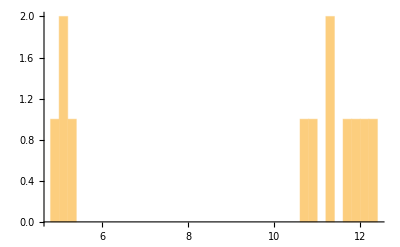

```mathematica
n=12;
dist=MixtureDistribution[{0.6,0.4}, {NormalDistribution[12,1],NormalDistribution[5,0.3]}];
σs=RandomVariate[dist,n];
Q= Orthogonalize[RandomReal[{-1,1},{n,n}]];
A=Q.DiagonalMatrix[σs].Qᵀ;
b=RandomReal[{-1,1},n];
Histogram[SingularValueList[A],40]
```

```mathematica
f[x_]:=0.5 x.A.x + x.b
x0=RandomReal[{-1,1},n];
FindMinimum[ f[x],{x, x0}]
xMMa = LinearSolve[A,-b]
f[xMMa]
```

{-0.276598,{x→{0.0168274,0.114819,0.0993702,0.0764642,0.022398,0.076904,0.0525805,0.114174,0.0269864,0.077661,-0.106067,0.0524415}}}

{0.0168274,0.114819,0.0993702,0.0764642,0.022398,0.076904,0.0525805,0.114174,0.0269864,0.077661,-0.106067,0.0524415}

-0.276598